## Setup the Le Roy potentials in van der Waals units

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μ=mLi7/2;
```

Change these next commands to read your local files for the singlet and triplet potentials:

```mathematica
singletdata=Import["~/Documents/GitHub/LiScattering/fort.10"];
tripletdata=Import["~/Documents/GitHub/LiScattering/fort.30"];
rmin=singletdata[[1,1]];
rmax = singletdata[[Length[singletdata],1]];
```

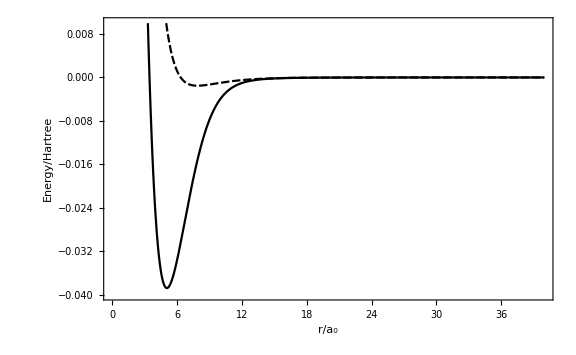

```mathematica
VSinglet = Interpolation[singletdata];
VTriplet = Interpolation[tripletdata];
Plot[{VSinglet[r],VTriplet[r]},{r,rmin,40},Frame->True,(*PlotRange->{-0.040,0.010}*)PlotRange->{-0.04,.01},ImageSize->Large,FrameLabel->{"r/a_0","Energy/Hartree"},LabelStyle->Large]
```

```mathematica
C6 = 6.71527 * 10^6(invcminHartree)(AngstrominBohr)^6
C8 = 1.12588 * 10^8(invcminHartree)(AngstrominBohr)^8
C10 = 2.78604 * 10^9(invcminHartree)(AngstrominBohr)^10
```

1393.39

83425.5

7.37211×10^6

```mathematica
Clear[β]
```

```mathematica
Vlr[r_]:=-C6/r^6-C8/r^8-C10/r^10;
Solve[Vlr[β]==-ℏ^2/(2μ β^2)/.ℏ->1,β]
```

{{β→-65.2049},{β→-4.62654-7.16445 ⅈ},{β→-4.62654+7.16445 ⅈ},{β→0.-64.7443 ⅈ},{β→0.+64.7443 ⅈ},{β→4.62654-7.16445 ⅈ},{β→4.62654+7.16445 ⅈ},{β→65.2049}}

```mathematica
β=β/.%[[Length[%]]]
```

65.2049

```mathematica
EVDV=1/(2μ β^2);Distribute[Vlr[r β]/EVDV]
```

-0.000288536/r^10-0.0138825/r^8-0.985829/r^6

```mathematica
VS[r]=VSinglet[r β]/EVDV;
VT[r]=VTriplet[r β]/EVDV;
Vlrvdv[r]=Vlr[r β]/EVDV;
```

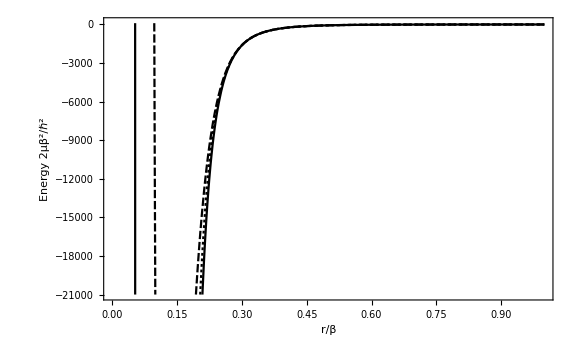

```mathematica
Plot[{VS[r],VT[r],Vlrvdv[r]},{r,.01,1},Frame->True,(*PlotRange->{-0.040,0.010}*)PlotRange->{-2.1 10^4,10^2},ImageSize->Large,FrameLabel->{"r/β","Energy 2μβ^2/ℏ^2"},LabelStyle->Large]
```

Calculate the inner turning points

```mathematica
rSinner=r/.FindRoot[VS[r],{r,.05}]
rTinner=r/.FindRoot[VT[r],{r,.05}]
```

0.052808

0.097099

```mathematica
DS=Abs[FindMinimum[{VS[r],rSinner≤r≤1},{r,.07}][[1]]]
DT=Abs[FindMinimum[{VT[r],rTinner≤r≤1},{r,0.1}][[1]]]
```

2.11007×10^6

82690.9

## Singlet/Triplet bound states (single-channel)

```mathematica
ℒt=-u''[x]+(VT[x]+DT)*u[x];
ℒS=-u''[x]+(VS[x]+DS)*u[x];
rmin=0.9rTinner;
rmax=3;
```

Find the 20 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{valsTriplet,funsTriplet}=NDEigensystem[ℒt,u[x],{x,rmin,rmax},20, Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->10^-4},"IntegrationOrder"->5}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«3»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsTriplet-DT
```

{-48542.3,-42764.1,-7321.73,-971.016,-48.0378,0.34813,3.34118,9.59267,19.054,31.6308,47.2598,65.9163,87.6138,112.403,140.371,171.645,206.389,244.807,287.119,333.513}

Visualize the eigenfunctions scaled by h and offset by the respective eigenvalue:

```mathematica
pvt=Plot[VT[x],{x,rmin,rmax},PlotRange->{-DT,0.001}];
p1=Plot[(Evaluate[100funsTriplet[[11;;11]]+valsTriplet[[11;;11]]-DT]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
```

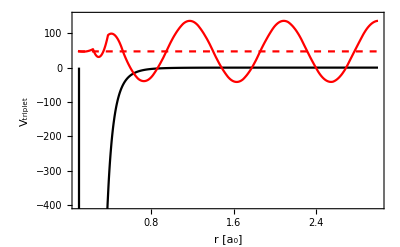

```mathematica
Show[{pvt,p1,Plot[valsTriplet[[11]]-DT,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{rmin,rmax},{-400,150}},FrameLabel->{"r [a_0]","V_triplet"}]
```

```mathematica
ℒs=-1/(2 μ)u''[x]+(VSinglet[x]+DeSinglet)*u[x];
```

```mathematica
{valsSinglet,funsSinglet}=NDEigensystem[ℒs,u[x],{x,rmin,rmax},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«1»,«3»,{1,{{«1»},{«1»}},{0.0000133333,-3.33333×10^-6,«14891045»,6.66666×10^-6,0.0000533333}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsSinglet-DeSinglet
```

{-0.0380075,-0.03643,-0.0348763,-0.0333466,-0.0318411,-0.0303601,-0.0289038,-0.0274725,-0.0260666,-0.0246865,-0.0233325,-0.0220052,-0.0207051,-0.0194327,-0.0181887,-0.0169737,-0.0157885,-0.014634,-0.013511,-0.0124206,-0.0113638,-0.0103419,-0.00935611,-0.00840795,-0.00749897,-0.00663089,-0.00580557,-0.00502506,-0.00429156,-0.00360748,-0.0029754,-0.00239807,-0.00187838,-0.00141933,-0.00102384,-0.000694537,-0.000433317,-0.000240368,-0.000112451,-0.0000404707,-7.73955×10^-6,6.22088×10^-6,0.0000272767,0.0000574498,0.000100942,0.000132881,0.000186305,0.000240224,0.000301443,0.000364063}

```mathematica
valsSinglet[[1;;41]]-DeSinglet
```

{-0.0380075,-0.03643,-0.0348763,-0.0333466,-0.0318411,-0.0303601,-0.0289038,-0.0274725,-0.0260666,-0.0246865,-0.0233325,-0.0220052,-0.0207051,-0.0194327,-0.0181887,-0.0169737,-0.0157885,-0.014634,-0.013511,-0.0124206,-0.0113638,-0.0103419,-0.00935611,-0.00840795,-0.00749897,-0.00663089,-0.00580557,-0.00502506,-0.00429156,-0.00360748,-0.0029754,-0.00239807,-0.00187838,-0.00141933,-0.00102384,-0.000694537,-0.000433317,-0.000240368,-0.000112451,-0.0000404707,-7.73955×10^-6}

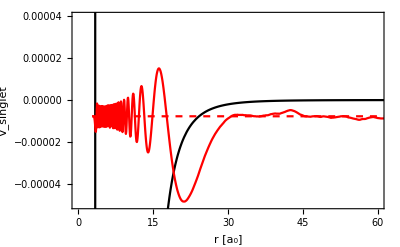

```mathematica
pvs=Plot[VSinglet[x],{x,rmin,rmax},PlotRange->{-DeSinglet,0.001}];
p2=Plot[(Evaluate[.0001funsSinglet[[41;;41]]+valsSinglet[[41;;41]]-DeSinglet]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
Show[{pvs,p2,Plot[valsSinglet[[41]]-DeSinglet,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{0,60},{-0.00005,0.00004}},FrameLabel->{"r [a_0]","V_singlet"}]
```

#### Milne equation

(-ℏ^2/(2μ)∂^2/(∂r^2)+(ℏ^2 l(l+1))/(2μ r^2)+V(r))ψ(r)=E ψ(r)

is written as:

(∂^2/(∂r^2)+(2μ)/ℏ^2(E-V(r)-(ℏ^2 l(l+1))/(2μ r^2)))ψ(r)=0

(∂^2/(∂r^2)+k^2(r))ψ(r)=0

Since we want V(r)→-C_6/r^6, we move to scaled units where the unit of length is β_6=(2μ C_6/ℏ^2)^(1/4) and energy is measured in units of ℏ^2/2μ β_6^2.

U(r)=V(r)+(ℏ^2 l(l+1))/(2μ r^2)→-1/r^6+(l(l+1))/r^2

So

k^2(r)=ϵ+1/r^6-(l(l+1))/r^2

Milne showed [W.E. Milne, Phys. Rev. 35, 863 (1930); Am. Math. Mon. 40, 322 (1933)] that the solution can be written

ψ(r)=a α(r) sin(∫_0^r α^-2(r')ⅆr'+b)

This result is valid provided that α(r) is any particular solution to Milne’s second-order, nonlinear differential equation:

(∂^2 α(r))/(∂r^2)+k^2(r)α(r)=1/(α^3(r))

### Energy Normalization

∫_0^∞ ⅆR R^2 j_l(k R) j_l(q R)=π/2(δ(k-q))/k^2

∫_0^∞ ⅆR f_l(k R) f_l(q R)=δ(E_k-E_q)

δ(E_k-E_q)=δ(k^2-q^2)=(δ(k-q))/(2q)=(δ(k-q))/(2k)=(δ(k-q))/(2 √(k q))

∫_0^∞ ⅆR R^2 j_l(k R) j_l(q R)=π/2(2k δ(E_k-E_q))/k^2

∫_0^∞ ⅆR R^2 j_l(k R) j_l(q R)=π(δ(E_k-E_q))/k

∫_0^∞ ⅆR R^2 j_l(k R) j_l(q R)=π/(√(k q)) δ(E_k-E_q)

∫_0^∞ ⅆR (√(k q))/π R^2 j_l(k R) j_l(q R)= δ(E_k-E_q)

∫_0^∞ ⅆR √(k/π)R j_l(k R) √(q/π)R j_l(q R)= δ(E_k-E_q)

```mathematica
U[l_,r_]:=VSinglet[r]+(l(l+1))/(2μ r^2)
ksqr[ϵ_,l_,r_]:=ϵ-(VSinglet[r]+(l(l+1))/(2μ r^2));
ϵtest=0.0000000000001;
ltest=0;
rx=3.5;
rf=20;
BC1[ϵ_,l_,r_]=Simplify[ksqr[ϵ,l,r]^(-1/4)];

BC2[ϵ_,l_,r_]=Simplify[D[ksqr[ϵ,l,r]^(-1/4),r]];

αsol=NDSolve[{D[α[r],{r,2}]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}]
```

{{α→InterpolatingFunction[…]}}

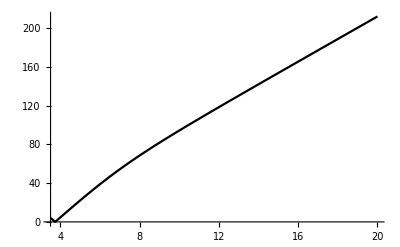

```mathematica
Plot[α[r]/.αsol[[1]],{r,rx,rf}]
```

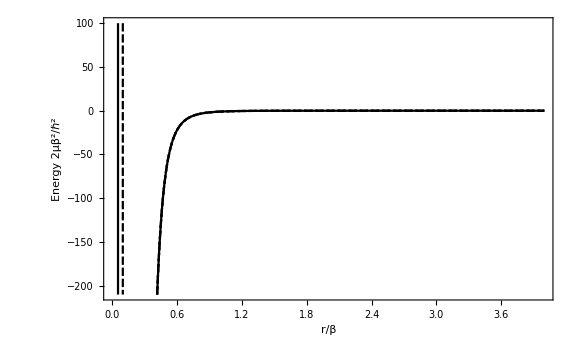
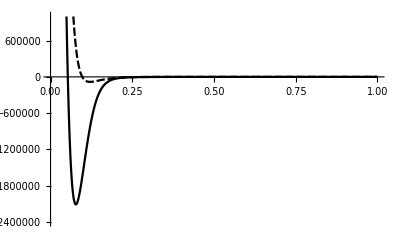
```mathematica
C6 = 6.71527 * 10^6(invcminHartree)(AngstrominBohr)^6
C8 = 1.12588 * 10^8(invcminHartree)(AngstrominBohr)^8
C10 = 2.78604 * 10^9(invcminHartree)(AngstrominBohr)^10
1393.3889292969122
83425.48021331812
7.372108056908806*^6
Vlr[r_]:=-C6/r^6-C8/r^8-C10/r^10;
Solve[Vlr[β]==-ℏ^2/(2μ β^2)/.ℏ->1,β]
Solve::ratnz: "Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result."
{{β->-65.20489291903131},{β->-4.6265432299700855-7.164448958583345 ⅈ},{β->-4.6265432299700855+7.164448958583345 ⅈ},{β->0.-64.74433726079533 ⅈ},{β->0.+64.74433726079533 ⅈ},{β->4.6265432299700855-7.164448958583345 ⅈ},{β->4.6265432299700855+7.164448958583345 ⅈ},{β->65.20489291903131}}
β=β/.%[[Length[%]]]
65.20489291903131
EVDV=1/(2μ β^2);Distribute[Vlr[r β]/EVDV]
-0.00028853610695099146/r^10-0.013882496186088318/r^8-0.9858289677069603/r^6
Plot[{VSinglet[r β]/EVDV,VTriplet[r β]/EVDV,Vlr[r β]/EVDV},{r,.01,4},Frame->True,(*PlotRange->{-0.040,0.010}*)PlotRange->{-2.1 10^2,10^2},ImageSize->Large,FrameLabel->{"r/β","Energy 2μβ^2/ℏ^2"},LabelStyle->Large]
-Graphics-
Create new interpolated potentials in van der Waals units
VSData=Transpose[{Transpose[singletdata][[1]]/β,Transpose[singletdata][[2]]/EVDV}];
VTData=Transpose[{Transpose[tripletdata][[1]]/β,Transpose[tripletdata][[2]]/EVDV}];
VS=Interpolation[VSData]
InterpolatingFunction[…]
VT=Interpolation[VTData]
InterpolatingFunction[…]
Plot[{VS[r],VT[r]},{r,0.01,1},PlotRange->{-2.4 10^6,10^6}]
-Graphics-
Calculate the inner turning points
rSinner=r/.FindRoot[VS[r],{r,.05}]
rTinner=r/.FindRoot[VT[r],{r,.05}]

0.052808036484131335
0.09709904614933515
DS=Abs[FindMinimum[{VS[r],rSinner≤r≤1},{r,.07}][[1]]]
DT=Abs[FindMinimum[{VT[r],rTinner≤r≤1},{r,0.1}][[1]]]
2.110074631365354*^6
82690.89490059657
Singlet/Triplet bound states (single-channel)

ℒt=-u''[x]+(VT[x]+DT)*u[x];
ℒS=-u''[x]+(VS[x]+DS)*u[x];
rmin=0.9rTinner;
rmax=3;

Find the 20 smallest eigenvalues and eigenfunctions on a refined mesh:
{valsTriplet,funsTriplet}=NDEigensystem[ℒt,u[x],{x,rmin,rmax},20, Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->10^-4},"IntegrationOrder"->5}}}];
Eigensystem::maxit2: "Warning: maximum number of iterations, \!\(\*RowBox[{\"1000\"}]\), has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help."
Eigensystem::chnpdef: "Warning: there is a possibility that the second matrix \!\(\*RowBox[{\"SparseArray\", \"[\", RowBox[{\"Automatic\", \",\", RowBox[{\"«\", \"3\", \"»\"}]}], \"]\"}]\) in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results."
valsTriplet-DT
{-48542.28992874955,-42764.12833195033,-7321.729059456673,-971.0157539341744,-48.037769331916934,0.3481297440303024,3.3411777256405912,9.592667735312716,19.053959125929396,31.630846207073773,47.25978770550864,65.91628548878361,87.61378748623247,112.40272139037552,140.37089703168022,171.6446705305425,206.3894705553539,244.80670723876392,287.1187663407618,333.5127209355851}
Visualize the eigenfunctions scaled byhand offset by the respective eigenvalue:
pvt=Plot[VT[x],{x,rmin,rmax},PlotRange->{-DT,0.001}];
p1=Plot[(Evaluate[100funsTriplet[[11;;11]]+valsTriplet[[11;;11]]-DT]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
Show[{pvt,p1,Plot[valsTriplet[[11]]-DT,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{rmin,rmax},{-400,150}},FrameLabel->{"r [a_0]","V_triplet"}]
-Graphics-
ℒs=-1/(2 μ)u''[x]+(VSinglet[x]+DeSinglet)*u[x];
{valsSinglet,funsSinglet}=NDEigensystem[ℒs,u[x],{x,rmin,rmax},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0001}}}}];
Eigensystem::maxit2: "Warning: maximum number of iterations, \!\(\*RowBox[{\"1000\"}]\), has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help."
Eigensystem::chnpdef: "Warning: there is a possibility that the second matrix \!\(\*RowBox[{\"SparseArray\", \"[\", RowBox[{\"Automatic\", \",\", RowBox[{\"«\", \"1\", \"»\"}], \",\", RowBox[{\"«\", \"3\", \"»\"}], \",\", RowBox[{\"{\", RowBox[{\"1\", \",\", RowBox[{\"{\", RowBox[{RowBox[{\"{\", RowBox[{\"«\", \"1\", \"»\"}], \"}\"}], \",\", RowBox[{\"{\", RowBox[{\"«\", \"1\", \"»\"}], \"}\"}]}], \"}\"}], \",\", RowBox[{\"{\", RowBox[{\"0.000013333327837487286`\", \",\", RowBox[{\"-\", \"3.333331959343156`*^-6\"}], \",\", RowBox[{\"«\", \"14891045\", \"»\"}], \",\", \"6.666663922453587`*^-6\", \",\", \"0.00005333331134049027`\"}], \"}\"}]}], \"}\"}]}], \"]\"}]\) in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results."
valsSinglet-DeSinglet
{-0.038007517434460444,-0.03643001857236867,-0.034876327060307154,-0.03334662479337461,-0.031841127767353025,-0.03036008340709112,-0.028903769439824686,-0.027472494848841716,-0.026066602473419954,-0.024686472554417065,-0.023332526636937547,-0.022005231511176275,-0.020705103126479562,-0.019432710608010943,-0.018188680583228797,-0.0169737020214764,-0.015788531731273373,-0.01463400057116485,-0.013511020353270238,-0.012420591368906803,-0.011363810449887924,-0.010341879500012276,-0.009356114475927355,-0.00840795484394687,-0.007498973559989346,-0.006630887588069817,-0.005805568836477537,-0.005025055092953951,-0.004291560009771038,-0.003607480306864981,-0.0029753969847410994,-0.002398065188323306,-0.0018783839247644568,-0.0014193308337318161,-0.001023835331582526,-0.0006945371246494109,-0.0004333171043489348,-0.00024036774363871832,-0.00011245095097720675,-0.00004047073577215232,-7.739554008220906*^-6,6.220883959635881*^-6,0.00002727672984974977,0.000057449816403855325,0.00010094244245167222,0.00013288094940958756,0.0001863046792263054,0.00024022436743764003,0.0003014427699679842,0.0003640627341981381}
valsSinglet[[1;;41]]-DeSinglet
{-0.038007517434460444,-0.03643001857236867,-0.034876327060307154,-0.03334662479337461,-0.031841127767353025,-0.03036008340709112,-0.028903769439824686,-0.027472494848841716,-0.026066602473419954,-0.024686472554417065,-0.023332526636937547,-0.022005231511176275,-0.020705103126479562,-0.019432710608010943,-0.018188680583228797,-0.0169737020214764,-0.015788531731273373,-0.01463400057116485,-0.013511020353270238,-0.012420591368906803,-0.011363810449887924,-0.010341879500012276,-0.009356114475927355,-0.00840795484394687,-0.007498973559989346,-0.006630887588069817,-0.005805568836477537,-0.005025055092953951,-0.004291560009771038,-0.003607480306864981,-0.0029753969847410994,-0.002398065188323306,-0.0018783839247644568,-0.0014193308337318161,-0.001023835331582526,-0.0006945371246494109,-0.0004333171043489348,-0.00024036774363871832,-0.00011245095097720675,-0.00004047073577215232,-7.739554008220906*^-6}
pvs=Plot[VSinglet[x],{x,rmin,rmax},PlotRange->{-DeSinglet,0.001}];
p2=Plot[(Evaluate[.0001funsSinglet[[41;;41]]+valsSinglet[[41;;41]]-DeSinglet]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
Show[{pvs,p2,Plot[valsSinglet[[41]]-DeSinglet,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{0,60},{-0.00005,0.00004}},FrameLabel->{"r [a_0]","V_singlet"}]
-Graphics-

(-ℏ^2/(2μ)∂^2/(∂r^2)+(ℏ^2 l(l+1))/(2μ r^2)+V(r))ψ(r)=E ψ(r)
is written as:
(∂^2/(∂r^2)+(2μ)/ℏ^2(E-V(r)-(ℏ^2 l(l+1))/(2μ r^2)))ψ(r)=0
(∂^2/(∂r^2)+k^2(r))ψ(r)=0
Since we wantV(r)->(-Subscript[C, 6])/r^6,we move to scaled units where the unit of length is Subscript[β, 6]=(2μ Subscript[C, 6]/ℏ^2)^(1/4)and energy is measured in units of ℏ^2/2μ Subscript[β, 6]^2 .
U(r)=V(r)+(ℏ^2 l(l+1))/(2μ r^2)->-1/r^6+(l(l+1))/r^2
So
k^2(r)=ϵ+1/r^6-(l(l+1))/r^2
Milne showed[W.E.Milne,Phys.Rev.35,863 (1930);Am.Math.Mon.40,322 (1933)] that the solution can be written
ψ(r)=a α(r) sin(∫_0^r α^-2(r')ⅆr'+b)
This result is valid provided thatα(r)is any particular solution to Milne’s second-order,nonlinear differential equation:
(∂^2 α(r))/(∂r^2)+k^2(r)α(r)=1/(α^3(r))
U[l_,r_]:=VSinglet[r]+(l(l+1))/(2μ r^2)
ksqr[ϵ_,l_,r_]:=ϵ-(VSinglet[r]+(l(l+1))/(2μ r^2));
ϵtest=0.0000000000001;
ltest=0;
rx=3.5;
rf=20;
BC1[ϵ_,l_,r_]=Simplify[ksqr[ϵ,l,r]^(-1/4)];

BC2[ϵ_,l_,r_]=Simplify[D[ksqr[ϵ,l,r]^(-1/4),r]];

αsol=NDSolve[{D[α[r],{r,2}]+ksqr[ϵtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,ltest,rx],α'[rx]==BC2[ϵtest,ltest,rx]},α,{r,rx,rf}]
{{α->InterpolatingFunction[…]}}
Plot[α[r]/.αsol[[1]],{r,rx,rf}]
-Graphics-
```